# Envariabel Projektarbete

## Felix Nilsson, Daniel Ahlsén, Simon Cederbom och Fredrik Assarsson

## Uppgift1

Det första problemet du stöter på är att detektorkondensatorns märkning är otydlig och du måste därför först bestämma dess kapacitans. Någon har redan på börjat detta arbete vilket resulterat i mätserien som finns i filen matserie.dat . Tabellen i filen visar spänningen (V) över kondensatorn som funktion av tiden (s) då den urladdas genom en resistor på 20.0 GΩ.

(a) Spänningen uC  över kondensatorn och strömmen i  genom resistorn vid tiden t .

 För att få fram spänningen och strömen vid tiden t, utnytjade vi sambandet at i + u/R= 0 och  i(t) = c_0* u'(t) för att få differentialekvationen c_0* u'(t)+ u 1/(R *c)= 0. Löser man den ser man att spänningen i kondensatorn avtar exponentiellt, u[t]=ⅇ^(-t/(R* c)) C[1]. Sedan kan man använda FindFit för få fram C_1= 251.707. Kör man sedan FindFit en andra gång med konstanten får man fram c_0= 3.27067×10^-11. För att få fram i(t) deriverade vi u(t) och stoppade in i formeln, i(t) = c_0* u'(t)  och fick D[251.707*ⅇ^(-t/(R*C0))]*C0 vilket ger i(t) = 8.23082×10^-9 ⅇ^(-1.52905 t)
  
 (b) Kondensatorns kapacitans C0 .
  c_0= 3.27067×10^-11, enligt a.

```mathematica
R=20*10^9;
DSolve[{u'[t]+u[t]*1/(R*c)==0}, u[t], t]
```

{{u[t]→ⅇ^(-t/(20000000000 c)) C[1]}}

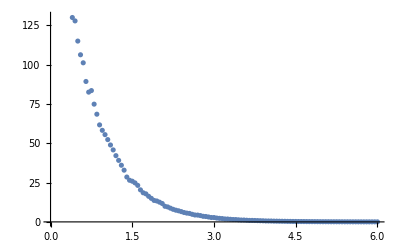

{a→251.707,b→1.52874}

```mathematica
Remove["Global`*"]
data=Import["/Users/Felix/GitHub/Envariabel-projekt/matserie.dat"];
ListPlot[data]
FindFit[data, a ⅇ^(- b x), {a,b}, x]
```

```mathematica
FindFit[data,251.70653701301623 ⅇ^(-t/(20000000000 c)) , c,t]
```

{c→3.27067×10^-11}

```mathematica
Remove["Global`*"]
R=20*10^9;
C0=3.27*10^-11;


D[251.707*ⅇ^(-t/(R*C0))]*C0
```

8.23082×10^-9 ⅇ^(-1.52905 t)

(c) Den tid t1  det tar innan kondensatorns laddning minskat till hälften.
Eftersom i(t) = q’(t), så kan man integrera i(t) för at få ut q(t). Kondensatorn när den är fullt laddad kommer då att innehålla q(0) Colomb. Detta gör att, om man löser ekvationen (q(0))/2 = q(t) med avsende på t kommer man att få tiden det tar för kondensatorn att bli av med halva sin laddning. Detta ger att tiden blir ≈0.45 s.

```mathematica
Remove["Global`*"]
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
q[t_]=Integrate[i[t],t]
Solve[q[0]/2==q[t],t]
```

-5.38296×10^-9 ⅇ^(-1.52905 t)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.453318}}

(d) Effektutvecklingen i resistorn vid tiden t.
P (t) = U(t) * I(t)

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
u[t_]=251.70653701301623 ⅇ^(-t/(20000000000 c)) ;
u[t]*i[t]
```

2.07175×10^-6 ⅇ^(-3.05779 t)

(e) Värmeenergin som utvecklats i resistorn under tiden t1  s och totala värmeenergin som utvecklats
då kondensatorn urladdats helt. Använd resultatet i (d).

För att lösa uppgiften utnytjade vi sambandet att Energin = Effekten * tiden. Effekten fick vi från förra uppgiften, då fick vi funktionen Energin(t) = 2.07175×10^-6 ⅇ^(-3.05779 t) t. För att sedan räkna ut hur totala mängden värmeenergi löste vi den genelariserade integralen: Limit[∫_0^R 2.07175×10^-6 ⅇ^(-3.05779 t) tⅆt,R→∞] →  2.21575×10^-7Joule.

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
u[t_]=251.70653701301623 ⅇ^(-t/(20000000000 c)) ;
p[t_]=u[t]*i[t];
En[t_]=p[t]*t
Limit[p[t],t->Infinity]
Limit[Integrate[En[t],{t,0,R}], R->Infinity]
```

2.07175×10^-6 ⅇ^(-3.05779 t) t

0.

2.21575×10^-7

## Uppgift 2

Spänningskällan du ska använda till larmet lämnar en konstant likspänning på 250 V. Amperemetern har en utgång som kan kopplas till en sirén och denna utgång aktiveras om strömmen är över 1.00 A under minst 250 s. Tjuvlarmet ska konstrueras så att det löser ut om kapacitansen förändras med mer än 10 %. Tiden det tar för kapacitansen att förändras.

(a) Förklara hur seriekretsen kan fungera som ett tjuvlarm.
När handen närmar sig kondensatorn kommer dennes kapacitans att öka vilket gör att kondensatorn laddas upp till sin nya maxladdning, detta i sin tur gör att en högre ström kommer att färdas i kretsen och leder till att ampermetern sätter igång högtalaren.

(b) Bestäm de värden på serieresistansen som uppfyller specifikationerna ovan.
Tips:  Mathematica-funktionerna DSolve  och Solve  kan användas här.
För att lösa vilken resistor som ska användas använde vi kirchhoffs spänningslag och utnytjade sambandet R*i+q/C= u_tot där vi utnytjade sambandet att i(t) = q’(t), för att få en differentialekvation, R* q'[t]+q[t]/c==250,q[0]==c0*250, begynnelsevilkoret för q(0)=c_0*250. Lösningen på diffekvationen ger oss q(t), vilket vid derivering ger q’(t) = i(t). Stoppar man sedan in tiden och den önskade strömmen kan man lösa ut resistansen. 
Svar: Den önskade resistansen ligger mellan 3.99964×10^6Ω och 1.3671×10^7Ω.

```mathematica
Remove["Global`*"]

DSolve[{r* q'[t]+q[t]/c==u,q[0]==c0*u},q[t],t];
FullSimplify[%]
```

{{q[t]→(c+(-c+c0) ⅇ^(-t/(c r))) u}}

```mathematica
Remove["Global`*"]
q[t_]=(c+(-c+c0) ⅇ^(-t/(c r))) u;
i[t_]=D[q[t],t];
FullSimplify[%]

c0=3.270666888845813*^-11;
c=c0*1.1;
u=250;
i[250*10^-6];
imin=1*10^-6;

Solve[i[250*10^-6]==imin,r];
FullSimplify[%]
```

((c-c0) ⅇ^(-t/(c r)) u)/(c r)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→3.99964×10^6},{r→1.3671×10^7}}

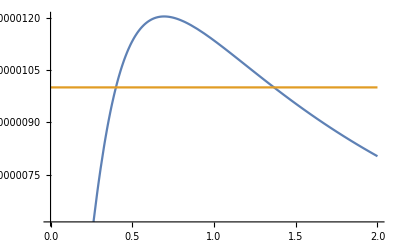

```mathematica
Plot[{i[250*10^-6],1*10^-6},{r, 0 , 20000000}]
```

(c) Förklara vad som händer om man väljer för stor respektive för liten resistans.
Väljer man en för stor resistor kommer man enligt Ohms lag att få en liten ström som alldrig kommer kunna lösa ut amperemetern.
Väljer man en för liten resistor kommer man få motsatt fenomen, en väldigt hög ström som löser larmet hela tiden.

## Uppgift 3

Antag nu att man vill öka känsligheten på larmet.

(a) Hur små kapacitansförändringar kan man mäta med ovanstående utrustning?
Tips: FindMaximum  och FindRoot  kan man ha nytta av här.

Först letar vi efter den optimala resistansen som kommer att vara den resistansensom ger högst ström.
För att hitta den minsta kapacitansförändringen man kan mäta, använder vi formeln för i(t)=((c-c0) ⅇ^(-t/(c r)) u)/(c r), där det ända som är okänt efter att vi stoppar in siffror c som är c0 * p, där p är en konstant som bestämmer hur många procent man måste justera kapasitansen för att kunna få en ström på 1μA under 250μ s.
Svar: 8.31859%

```mathematica
Remove["Global`*"]
i[t_]=D[DSolve[{r* q'[t]+q[t]/c1==u, q[0]==c0*u},q[t],t][[1]][[1]][[2]],t];
FullSimplify[%]

c0=3.270666888845813*^-11;
c1=c0 *1.1;
c=c0*p;
t=250*10^-6;
imin =1*10^-6;
u=250;

rMax=3.999639258464372*^6;
rMin=1.3670995185686743*^7;
rOpt=FindMaximum[i[250*10^-6],{r,rMax,rMin}][[2]][[1]][[2]];



Solve[((c-c0)ⅇ^(-t/(c rOpt)) u)/(c rOpt)==imin, p]
```

((-c0+c1) ⅇ^(-t/(c1 r)) u)/(c1 r)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→1.08319}}

(b) Vilken spänning krävs om larmet ska kunna detektera kapacitansförändringar ner till 5% ?

För att lösa denna använder vi samma formel för i(t) som i 3a men justerar så att kapacitansen i c är c0 + 5%, där den  enda okända u för spänning, löser man ut u får man att spänningen som krävs 416.7V.
Svar: 416.7V

```mathematica
Remove["Global`*"]
c0=3.270666888845813*^-11;
c=c0*1.05;
rOpt=6.765316622668311*^6;
imin =1*10^-6;
t=250*10^-6;
Solve[((c-c0)ⅇ^(-t/(c rOpt)) u)/(c rOpt)==imin, u]
```

{{u→416.7}}